### Sample WARC File

```mathematica
sampleWARCFile="/Users/ianmilligan1/dropbox/git/warcbase-resources/Sample-Data/ARCHIVEIT-227-QUARTERLY-XUGECV-20091218231727-00039-crawling06.us.archive.org-8091.warc.txt";
```

```mathematica
wFile=OpenRead[sampleWARCFile]
```

InputStream[…]

### Function to parse record into an Association

```mathematica
recordToAssociation[rec_]:=
Module[{recmod,fields,vals},
recmod=StringReplace[rec,"\r\n\r\n"->"\r\n\r\nCONTENT: "];
fields=StringTrim[StringExtract[StringSplit[recmod,"\r"],":"->1]];
vals=Map[StringTrim[StringReplace[#,Shortest[StartOfString~~Except[":"]..]~~":"->""]]&,StringSplit[recmod,"\r"]];
Return[Association[DeleteCases[MapThread[Rule,{fields,vals}],Rule["",""]|Rule["CONTENT",""]]]]]
```

### Jump to beginning of stream

```mathematica
SetStreamPosition[wFile,1]
```

1

### Get first record

```mathematica
tempRecord=Read[wFile,Record,RecordSeparators->{"WARC/1.0" }];
```

```mathematica
tempRecordAssociation=recordToAssociation[tempRecord];
```

```mathematica
Keys[tempRecordAssociation]
```

{WARC-Type,WARC-Target-URI,WARC-Date,WARC-Concurrent-To,WARC-Record-ID,Content-Type,Content-Length,CONTENT,User-Agent,From,Connection,Referer,Host,Cookie}

```mathematica
tempRecordAssociation["Host"]
```

Missing[KeyAbsent,Host]

```mathematica
tempRecordAssociation["WARC-Type"]
```

request

```mathematica
tempRecordAssociation["WARC-Date"]
```

2009-12-18T23:17:11Z

```mathematica
tempRecordAssociation["WARC-Filename"]
```

Missing[KeyAbsent,WARC-Filename]

N.B. This isn’t working perfectly right now, because if there is no CONTENT, following field is subsumed in it

```mathematica
tempRecordAssociation["Content-Length"]
```

2937

```mathematica
tempRecordAssociation["CONTENT"]
```

GET /videoplayback?ip=0.0.0.0&sparams=id%2Cexpire%2Cip%2Cipbits%2Citag%2Calgorithm%2Cburst%2Cfactor&fexp=905207&algorithm=throttle-factor&itag=34&ipbits=0&burst=40&sver=3&expire=1261202400&key=yt1&signature=D720E06EA04837A369862A97B1CA473A0B24EEAE.CB03D85025EA6B66183212AC5635D5CABE2D6B40&factor=1.25&id=1ab944435e6654f3 HTTP/1.0

### Get second record

```mathematica
tempRecord=Read[wFile,Record,RecordSeparators->{"WARC/1.0" }]
```

```mathematica
tempRecordAssociation=recordToAssociation[tempRecord];
```

```mathematica
Keys[tempRecordAssociation]
```

{WARC-Type,WARC-Target-URI,WARC-Date,WARC-Concurrent-To,WARC-Record-ID,Content-Type,Content-Length,CONTENT,User-Agent,From,Connection,Referer,Host,Cookie}

```mathematica
tempRecordAssociation["WARC-Target-URI"]
```

http://v7.lscache3.c.youtube.com/videoplayback?ip=0.0.0.0&sparams=id%2Cexpire%2Cip%2Cipbits%2Citag%2Calgorithm%2Cburst%2Cfactor&fexp=905207&algorithm=throttle-factor&itag=34&ipbits=0&burst=40&sver=3&expire=1261202400&key=yt1&signature=D720E06EA04837A369862A97B1CA473A0B24EEAE.CB03D85025EA6B66183212AC5635D5CABE2D6B40&factor=1.25&id=1ab944435e6654f3

In this case the CONTENT field works as we want

```mathematica
tempRecordAssociation["CONTENT"]
```

GET /videoplayback?ip=0.0.0.0&sparams=id%2Cexpire%2Cip%2Cipbits%2Citag%2Calgorithm%2Cburst%2Cfactor&fexp=905207&algorithm=throttle-factor&itag=34&ipbits=0&burst=40&sver=3&expire=1261202400&key=yt1&signature=D720E06EA04837A369862A97B1CA473A0B24EEAE.CB03D85025EA6B66183212AC5635D5CABE2D6B40&factor=1.25&id=1ab944435e6654f3 HTTP/1.0

### Get next 10 filenames

```mathematica
Do[
tempRecord=Read[wFile,Record,RecordSeparators->{"WARC/1.0" }];
tempRecordAssociation=recordToAssociation[tempRecord];
Print[tempRecordAssociation["WARC-Target-URI"]],10]
```

Missing[KeyAbsent,WARC-Target-URI]

http://v7.lscache3.c.youtube.com/videoplayback?ip=0.0.0.0&sparams=id%2Cexpire%2Cip%2Cipbits%2Citag%2Calgorithm%2Cburst%2Cfactor&fexp=905207&algorithm=throttle-factor&itag=34&ipbits=0&burst=40&sver=3&expire=1261202400&key=yt1&signature=D720E06EA04837A369862A97B1CA473A0B24EEAE.CB03D85025EA6B66183212AC5635D5CABE2D6B40&factor=1.25&id=1ab944435e6654f3

http://v7.lscache3.c.youtube.com/videoplayback?ip=0.0.0.0&sparams=id%2Cexpire%2Cip%2Cipbits%2Citag%2Calgorithm%2Cburst%2Cfactor&fexp=905207&algorithm=throttle-factor&itag=34&ipbits=0&burst=40&sver=3&expire=1261202400&key=yt1&signature=D720E06EA04837A369862A97B1CA473A0B24EEAE.CB03D85025EA6B66183212AC5635D5CABE2D6B40&factor=1.25&id=1ab944435e6654f3

http://www.davidsuzuki.org/_pvw370829/Publications/Drive_Green.asp

http://www.davidsuzuki.org/_pvw370829/Publications/Drive_Green.asp

http://www.davidsuzuki.org/_pvw370829/Publications/Drive_Green.asp

http://www.equalvoice.ca/images/images/french/js/images/sponsors/enbridge.jpg

http://www.equalvoice.ca/images/images/french/js/images/sponsors/enbridge.jpg

http://www.equalvoice.ca/images/images/french/js/images/sponsors/enbridge.jpg

http://www.liberal.ca/share_e.aspx?link=http://www.liberal.ca/en/newsroom/liberal-tv/category/56E6B9156BA42F5F_events/4.36363636364/ZSj39F5L1rM~hommage-a-ceux-qui-ont-servi

```mathematica
? StreamPosition
```

StreamPosition[stream] returns an integer that specifies the position of the current point in an open stream.

```mathematica
StreamPosition[wFile]
```

4475

Process Content of WARC as Stream

```mathematica
trial=Reap[
While[(tempRecord=Read[wFile,Record,RecordSeparators->{"WARC/1.0"}])=!=EndOfFile,tempRecordAssociation=recordToAssociation[tempRecord];
Sow[tempRecordAssociation["Host"]];
]];
```

```mathematica
frequency=Tally[Cases[Flatten[trial⟦2⟧],Except[_Missing]]]
```

{{v7.lscache3.c.youtube.com,2},{www.davidsuzuki.org,1689},{www.equalvoice.ca,4644},{www.liberal.ca,1968},{www.canadiancrc.com,154},{www.greenparty.ca,15},{greenparty.ca,869},{www.ndp.ca,447},{www.fairvote.ca,465},{www.policyalternatives.ca,596},{podcast.cbc.ca,1},{farm3.static.flickr.com,4},{youtube.com,7},{img.youtube.com,7},{images.ctv.ca,1},{www.partivert.ca,22},{www.gca.ca,2},{www.communitywalk.com,2},{www.flickr.com,1},{vimeo.com,2},{www.oee.nrcan.gc.ca,2},{naturechallenge.org,2},{e-activist.com,2},{www.e-activist.com,2},{www.naturechallenge.org,1},{www.youtube.com,2},{v18.lscache5.c.youtube.com,2},{xfer.ndp.ca,1},{www.cbs.com,1},{v2.cache7.c.youtube.com,1}}

```mathematica
PieChart[frequency[[All,2]],ChartLabels->frequency[[All,1]]]
```

-Graphics-

-Graphics-

```mathematica
SetStreamPosition[wFile,1]
```

1

```mathematica
content=Reap[
While[(tempRecord=Read[wFile,Record,RecordSeparators->{"WARC/1.0"}])=!=EndOfFile,tempRecordAssociation=recordToAssociation[tempRecord];
Sow[tempRecordAssociation["CONTENT"]];
]];
```

```mathematica
Head[content]
```

List

```mathematica
Length[content]
```

2

```mathematica
Flatten[content⟦2⟧]⟦900⟧
```

via: http://www.liberal.ca/en/newsroom/liberal-tv/category/DF12BDD4BB96EFE8_tv-ads/4.36363636364/tcyFdwoWBAY~jobs--emplois-en

```mathematica
SetStreamPosition[wFile,1];
contentType=Reap[
While[(tempRecord=Read[wFile,Record,RecordSeparators->{"WARC/1.0"}])=!=EndOfFile,tempRecordAssociation=recordToAssociation[tempRecord];
Sow[tempRecordAssociation["CONTENT"]];
]];
(**frequency=Tally[Cases[Flatten[contentType⟦2⟧],Except[_Missing]]]**)
```

```mathematica
contentType[[1]]
```

```mathematica
Length[contentType]
```

2

```mathematica
content=Flatten[contentType⟦2⟧];
```

```mathematica
Length[content]
```

32759

```mathematica
? Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.

```mathematica
StringReplace["<title>The Title</title>
 <h1>The <a href='link'>head</a></h1>
 <p>Some text follows here...</p>","<"~~Except[">"]..~~">"->""]
```

```mathematica
stripped=StringReplace[content,"<"~~Except[">"]..~~">"->""];
```

```mathematica
Export["/users/ianmilligan1/desktop/stripped.txt",stripped];
```

```mathematica
list=StringSplit[stripped];
```

```mathematica
words=Flatten[list];
```

```mathematica
Short[words]
```

{software:,Heritrix/1.15.4,http://crawler.archive.org,«1356385»,of,Canada.}

```mathematica
(* match on text/html content *)
```

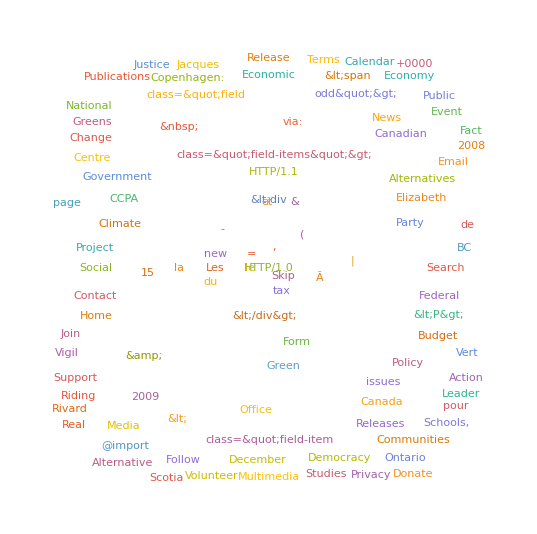

```mathematica
WordCloud[DeleteStopwords[words]]
```

```mathematica
bob={"ian","chuck","ian&","&ian"}
```

{ian,chuck,ian&,&ian}

```mathematica
DeleteCases[bob,"i"~~__~~"n"]
```

{ian,chuck,ian&,&ian}

```mathematica
Select[bob,StringFreeQ[#,___~~"&"~~___]&]
```

{ian,chuck}

```mathematica
cleaned=
Select[
Select[
Select[
Select[
Select[
Select[words,StringFreeQ[#,___~~"&"~~___]&]
,StringFreeQ[#,___~~"/"~~___]&]
,StringFreeQ[#,___~~"@"~~___]&]
,StringFreeQ[#,___~~":"~~___]&]
,StringFreeQ[#,___~~"+"~~___]&]
,StringLength[#]>1&];
```

```mathematica
efficient=ToLowerCase[
Select[
Select[words,StringFreeQ[#,{___~~"&"~~___,___~~"/"~~___,___~~"@"~~___,___~~":"~~___,___~~"+"~~___}]&]
,StringLength[#]>1&]];
```

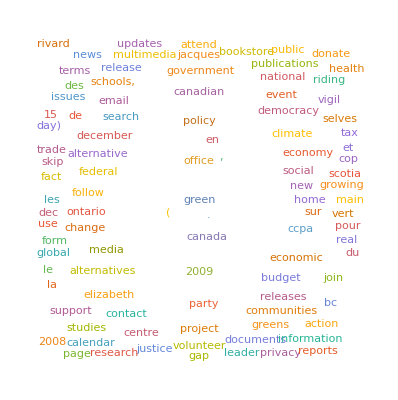

-Graphics-

```mathematica
WordCloud[DeleteStopwords[efficient]]
```